Harlan Brawer, 704924872, harlanbrawer@gmail.com, hw4

```mathematica
(* 1 *)
y1[x_,t_]=A1 Sin[k1 (x-v t)];
y2[x_,t_]=A2 Sin[k2 (x+v t)];
yr[x_,t_]=y1[x,t]+y2[x,t];
δk = 1;
k2=k1+δk;
v=1;
k1=2*π;
A1=1;
A2=1;
Animate[
Plot[{y1[x,t],y2[x,t],yr[x,t]},{x,0,10}],
{t,0,10}
]
```

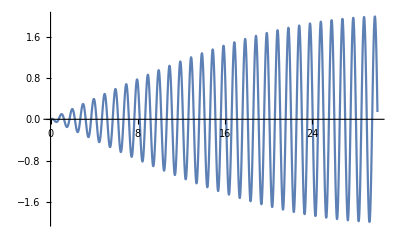

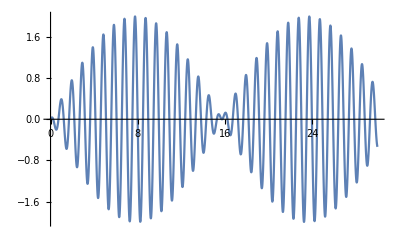

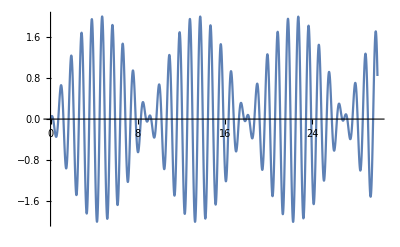

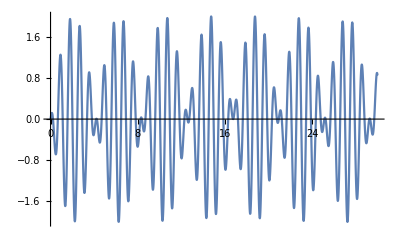

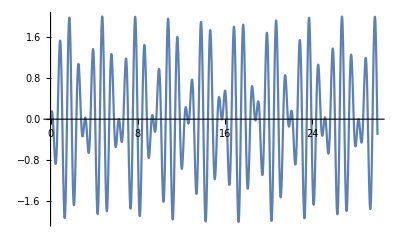

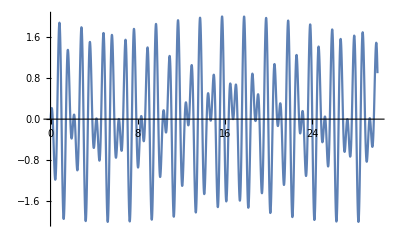

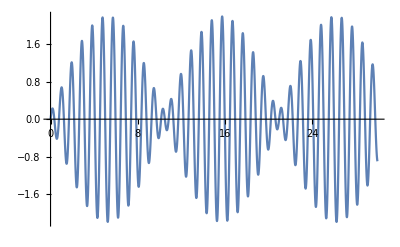

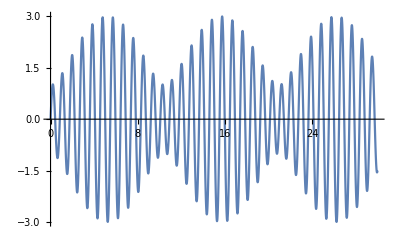

you would hear a beat

```mathematica
(* 2 *)
(* i *)
y1[x_,t_]:=A1 Sin[k1 (x-v t)];
y2[x_,t_]:=A2 Sin[k2 (x+v t)];
yr[x_,t_]:=y1[x,t]+y2[x,t];
k2:=k1+δk;
v=1;
k1=2*π;
A1=1;
A2=1;
δk=0.1;
Plot[yr[0,t],{t,0,30}]
δk=0.4;
Plot[yr[0,t],{t,0,30}]
δk=0.7;
Plot[yr[0,t],{t,0,30}]
δk=1.5;
Plot[yr[0,t],{t,0,30}]
δk=2.0;
Plot[yr[0,t],{t,0,30}]
δk=3.0;
Plot[yr[0,t],{t,0,30}]

(* ii *)
δk = .6;
A1 = 1;
A2=1.2;
Plot[yr[0,t],{t,0,30}]
A2=2.0;
Plot[yr[0,t],{t,0,30}]
A2=5.0;
Plot[yr[0,t],{t,0,30}]
A2=6.0;
Plot[yr[0,t],{t,0,30}]

(* iii *)
Print["you would hear a beat"]
A1=1;
A2=2;
δk=0.5;
Animate[
Plot[
yr[x,t],
{x,0,10}],
{t,0,10}]
```

```mathematica
(* 3 *)
Remove["Global`*"]//Quiet

$Assumptions={Element[{A,Ω,ω,t},Reals] && A>0 && Ω>0 && ω>0};
k0 = 1;
Δk=2;

A[k_] = DiracDelta[k-k0];
c[k_] = FourierTransform[A[k],k,t]//Simplify

A[k_] = Piecewise[{{1,Abs[k-k0]<Δk}},0];
c[k_] = FourierTransform[A[k],k,t]//Simplify

A[k_] = Piecewise[{{Cos[π*(kk-k0)/(2*Δk)],Abs[k-k0]<Δk}}];
c[k_] = FourierTransform[A[k],k,t]//Simplify

A[k_] = Piecewise[{{(k-k0+Δk)/(2*Δk),Abs[k-k0]<Δk}}];
c[k_] = FourierTransform[A[k],k,t]//Simplify

A[k_] = Piecewise[{{(k-k0)^2/(Δk)^2,Abs[k-k0]<Δk}}];
c[k_] = FourierTransform[A[k],k,t]//Simplify
```

ⅇ^(ⅈ t)/(√(2 π))

(2 √(2/π) Cos[t] (Cos[t]+ⅈ Sin[t]) Sin[t])/t

(2 √(2/π) Cos[1/4 (-1+kk) π] Cos[t] (Cos[t]+ⅈ Sin[t]) Sin[t])/t

(ⅇ^(-ⅈ t) (-1+ⅇ^(4 ⅈ t) (1-4 ⅈ t)))/(4 √(2 π) t^2)

(ⅇ^(ⅈ t) (2 t Cos[2 t]+(-1+2 t^2) Sin[2 t]))/(√(2 π) t^3)

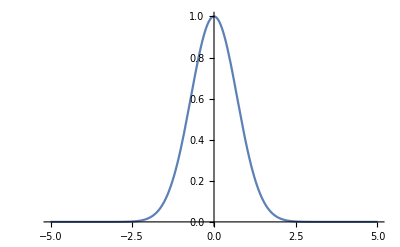

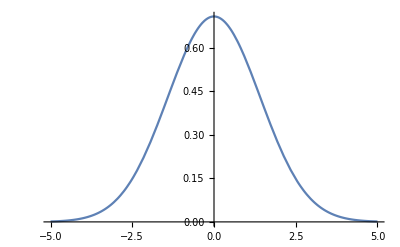

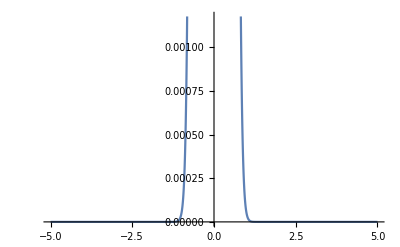

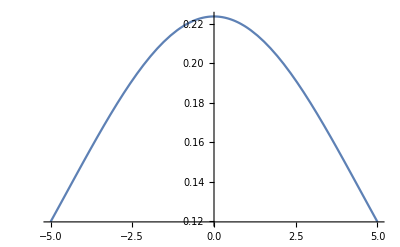

-(√(2/π) Sin[a k] (-1+UnitStep[-a]))/k

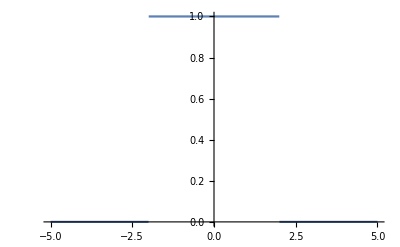

$Aborted

```mathematica
(* 5 *)
Remove["Global`*"]//Quiet
f[x_]:=n*E^(-α*x^2);
A[k_]:=FourierTransform[f[x],x,k];
n=1;
α=1;
Plot[f[x],{x,-5,5}]
Plot[A[k],{k,-5,5}]
α=10;
Plot[f[x],{x,-5,5}]
Plot[A[k],{k,-5,5}]

f[x_]:=Piecewise[{{1,Abs[x]<a},{0,Abs[x]≥a}}]
A[k_]:=FourierTransform[f[x],x,k];
a=2;
Plot[f[x],{x,-5,5}]
Plot[A[k],{k,-5,5}]
```

```mathematica
(* 6 *)
Remove["Global`*"]//Quiet

$Assumptions={Element[{A,Ω,ω,t},Reals] && A>0 && Ω>0 && ω>0};

F[t_] = A Sin[Ω t];
G[t_] = A Sin[Ω t]*Sin[ω2 t];
H[t_] = A Sin[Ω t];

c[ω_] = FourierTransform[F[t],t,ω]//Simplify
c[ω_] = FourierTransform[G[t],t,ω]//Simplify
c[ω_] = FourierTransform[H[t],t,ω]//Simplify
```

ⅈ A √(π/2) DiracDelta[ω-Ω]

-1/2 A √(π/2) DiracDelta[ω-Ω-ω2]+1/2 A √(π/2) DiracDelta[ω+Ω-ω2]+1/2 A √(π/2) DiracDelta[ω-Ω+ω2]-1/2 A √(π/2) DiracDelta[ω+Ω+ω2]

ⅈ A √(π/2) DiracDelta[ω-Ω]